```mathematica
phasePortrait:=Function[{A,B},
Labeled[StreamPlot[{
x(A[[1,1]]y+A[[1,2]](1-y)-(A[[1,1]]x y+A[[1,2]]x(1-y)+A[[2,1]](1-x)y+A[[2,2]](1-x)(1-y))),
y(B[[1,1]]x+B[[1,2]](1-x)-(B[[1,1]]x y+B[[1,2]]y(1-x)+B[[2,1]](1-y)x+B[[2,2]](1-y)(1-x)))},{x,0,1},{y,0,1}],{"A="*MatrixForm[A], "   B="*MatrixForm[B]}]]
A={{0,-10},{13,0}};
B={{0,-5},{3,0}};
```

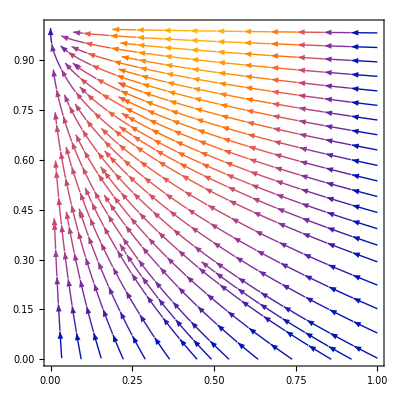
-Graphics-{A= (0 | 0
1 | 0),   B= (0 | 0.5
0 | 0)}

```mathematica
(*fig. 1a*)
A={{0,0},{1,0}};
B={{0,0.5},{0,0}};
phasePortrait[A,B]
```

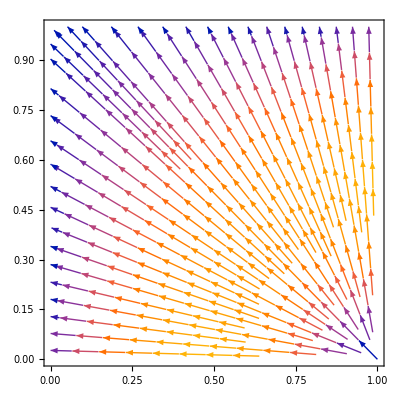
-Graphics-{A= (0 | -1
0 | 0),   B= (1 | 0
0 | 0)}

```mathematica
(*fig. 1b*)
A={{0,-1},{0,0}};
B={{1,0},{0,0}};
phasePortrait[A,B]
```

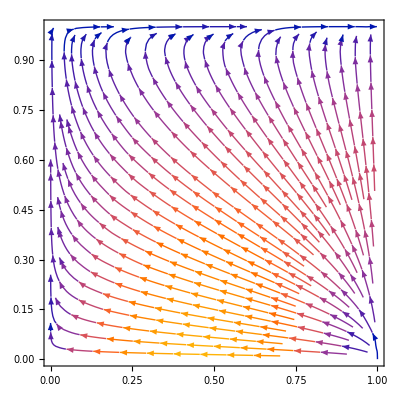
-Graphics-{A= (2 | -10
0 | 15),   B= (2 | 0
-10 | -5)}

```mathematica
(*fig. 2a*)
A={{2,-10},{0,15}};
B={{2,0},{-10,-5}};
phasePortrait[A,B]
```

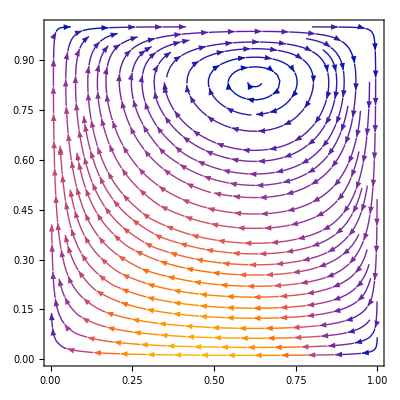
-Graphics-{A= (2 | 5
0 | 15),   B= (2 | 0
5 | -5)}

```mathematica
(*fig. 2b*)
A={{2,5},{0,15}};
B={{2,0},{5,-5}};
phasePortrait[A,B]
```

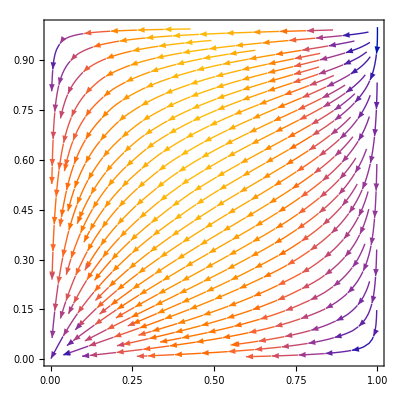
-Graphics-{A= (0.5 | -1
2 | 0),   B= (0.5 | -1
1 | 0)}

```mathematica
(*fig. 3a*)
A={{0.5, -1},{2,0}};
B={{0.5,-1},{1,0}};
phasePortrait[A,B]
```

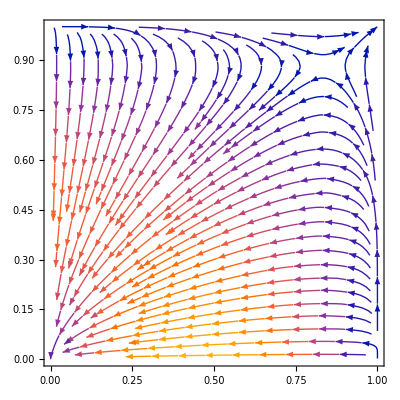
-Graphics-{A= (2 | -10
0 | 5),   B= (2 | -5
0 | 5)}

```mathematica
(*fig. 3b*)
A={{2, -10},{0,5}};
B={{2,-5},{0,5}};
phasePortrait[A,B]
```